```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
data = Import["../../runs/Trials/N9K9/81027575.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
cmatdata = Monitor[Table[cMatOne[data[[kk]]], {kk, 1, Length[data]}], ProgressIndicator[(kk-1)/(Length[data]-1)]];
```

```mathematica
simEig = Flatten[Eigenvalues/@cmatdata[[All, 2]]];
```

```mathematica
randEig = With[{randMats = (# - 1/($N)Tr[#]*IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[$N], 100000]}, Flatten[Eigenvalues/@randMats]];
```

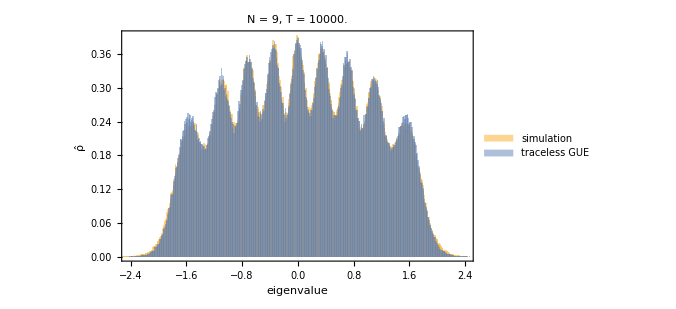

```mathematica
Histogram[{Standardize[simEig], Standardize[randEig]}, 400, PDF,
Frame->True,
FrameStyle->Black,
FrameLabel->{"eigenvalue", "ρ̂"},
ChartLegends->{"simulation", "traceless GUE"},
ImageSize->500,
PlotLabel->Style["N = "<>ToString@$N<>", T = "<>ToString[0.1*Length[data]]]
]
```

```mathematica
trX1X2 = Tr[#[[2]].#[[3]]]&/@cmatdata//Chop;
```

```mathematica
{X1, X2} = Partition[RandomVariate[GaussianUnitaryMatrixDistribution[$N], 200000], 100000];
```

```mathematica
trX1X2rand = Tr[#[[1]].#[[2]]]&/@Thread[{X1, X2}]//Chop;
```

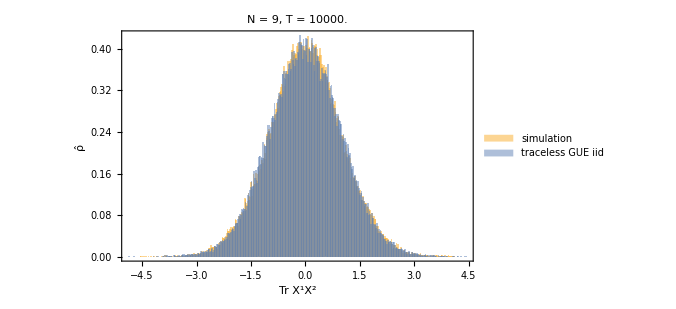

```mathematica
Histogram[{Standardize[trX1X2], Standardize[trX1X2rand]}, 400, PDF,
Frame->True,
FrameStyle->Black,
FrameLabel->{"Tr X^1X^2", "ρ̂"},
ChartLegends->{"simulation", "traceless GUE iid"},
ImageSize->500,
PlotLabel->Style["N = "<>ToString@$N<>", T = "<>ToString[0.1*Length[data]]]
]
```